```mathematica
Clear[x,m,y]
```

```mathematica
e1=y^2-(x^2-1)(x^2-l)(x^2-m)/.{l->c1*(c2-1)/(c1-1)/c2,m->c1/c2}
```

-((-1+x^2) (-c1/c2+x^2) (-(c1 (-1+c2))/((-1+c1) c2)+x^2))+y^2

```mathematica
e1/.{x^2->x}/.{x->(c2-c1)/c2 x+1,y->0}//Factor
```

-((-c1+c2)^3 x (1+x) (-1-x+c1 x))/((-1+c1) c2^3)

```mathematica
{c1*(c2-1)/(c1-1)/c2,c1/c2}/.{c1->-13/14,c2->5}//InputForm
```

{52/135, -13/70}

```mathematica
s=l1+l2
```

l1+l2

```mathematica
m=l1 l2
```

l1 l2

```mathematica
s/.{l1->1-l1,l2->1-l2}
```

2-l1-l2

```mathematica
m/.{l1->1-l1,l2->1-l2}
```

(1-l1) (1-l2)

```mathematica
((1-s)^2/.{l1->1-l1,l2->1-l2})-(1-s)^2//Factor
```

0

```mathematica
(s-2m/.{l1->1-l1,l2->1-l2})-(s-2m)//Factor
```

0

```mathematica
x=(1-s)^2
```

(1-l1-l2)^2

```mathematica
y=s-2m
```

l1+l2-2 l1 l2

```mathematica
(1-s)^2
```

(1-l1-l2)^2

```mathematica
(1-l1-l2)^2/.{l1->1}
```

l2^2

```mathematica
x/.{l1->1/l1,l2->1/l2}//Factor
```

(-l1-l2+l1 l2)^2/(l1^2 l2^2)

```mathematica
y
```

l1+l2-2 l1 l2

```mathematica
s/m
```

(l1+l2)/(l1 l2)

```mathematica
w
```

w

```mathematica
s/.{l1->1/(1-l1),l2->1/(1-l2)}//Factor
```

-(-2+l1+l2)/((-1+l1) (-1+l2))

```mathematica
ims=(2-s)/(1-s+m)//Factor
```

-(-2+l1+l2)/((-1+l1) (-1+l2))

```mathematica
imss=ims/.{l1->1/(1-l1),l2->1/(1-l2)}//Factor
```

(-l1-l2+2 l1 l2)/(l1 l2)

```mathematica
imss/.{l1->1/(1-l1),l2->1/(1-l2)}//Factor
```

l1+l2

```mathematica
m/.{l1->1/(1-l1),l2->1/(1-l2)}//Factor
```

1/((-1+l1) (-1+l2))

```mathematica
imm=1/(1-s+m)//Factor
```

1/((-1+l1) (-1+l2))

```mathematica
s+ims//Factor
```

(2-l1^2-2 l1 l2+l1^2 l2-l2^2+l1 l2^2)/((-1+l1) (-1+l2))

```mathematica
m+imm//Factor
```

(1+l1 l2-l1^2 l2-l1 l2^2+l1^2 l2^2)/((-1+l1) (-1+l2))

```mathematica
s ims//Factor
```

-((-2+l1+l2) (l1+l2))/((-1+l1) (-1+l2))

```mathematica
m imm//Factor
```

(l1 l2)/((-1+l1) (-1+l2))

```mathematica
/.{l1->1/(1-l1),l2->1/(1-l2)}
```

```mathematica
(a s+b m+e)/(c s+d m+f)/.{f->d}/.{d->-2 c}//Factor
```

-(e+a l1+a l2+b l1 l2)/(c (2-l1-l2+2 l1 l2))

```mathematica
(a s+b m+e)/(c s+d m+f)/.{l1->1/(1-l1),l2->1/(1-l2)}/.{f->d}/.{d->-2 c}//Factor
```

-(2 a+b+e-a l1-e l1-a l2-e l2+e l1 l2)/(c (2-l1-l2+2 l1 l2))

```mathematica
2 c+2 d==d
```

2 c+2 d==d

```mathematica
Solve[2 c+2 d==d,d]
```

{{d→-2 c}}

```mathematica
m
```

l1 l2

```mathematica
M={{1,-1,1},{2,-1,0},{1,0,0}}
```

{{1,-1,1},{2,-1,0},{1,0,0}}

```mathematica
M.{z0,z1,z2}
```

{z0-z1+z2,2 z0-z1,z0}

```mathematica
Eigensystem[M//Transpose]
```

{{1,1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3)},{{2,-1,2},{1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3),1},{1/2 (-1-ⅈ √3),1/2 (-1+ⅈ √3),1}}}

```mathematica
{2,-1,2}.{z0,z1,z2}/.{z0->z0-z1+z2,z1->2 z0-z1,z2->z0}//Factor
```

2 z0-z1+2 z2

```mathematica
s1=2 z0-z1+2 z2
```

2 z0-z1+2 z2

```mathematica
({1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3),1}.{z0,z1,z2})({1/2 (-1-ⅈ √3),1/2 (-1+ⅈ √3),1}.{z0,z1,z2})//Expand
```

z0^2-z0 z1+z1^2-z0 z2-z1 z2+z2^2

```mathematica
s2=z0^2-z0 z1+z1^2-z0 z2-z1 z2+z2^2
```

z0^2-z0 z1+z1^2-z0 z2-z1 z2+z2^2

```mathematica
t3=(z0-z1) (z0-z2) (z1-z2)
```

(z0-z1) (z0-z2) (z1-z2)

```mathematica
s3=(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2)
```

(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2)

```mathematica
({1/2 (-1+ⅈ √3),1/2 (-1-ⅈ √3),1}.{z0,z1,z2})^3+({1/2 (-1-ⅈ √3),1/2 (-1+ⅈ √3),1}.{z0,z1,z2})^3//Factor
```

(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2)

```mathematica
27s3^2+ t3^2-4 s2^3//Factor
```

104 (z0^3-z0^2 z1-2 z0 z1^2+z1^3-2 z0^2 z2+6 z0 z1 z2-z1^2 z2-z0 z2^2-2 z1 z2^2+z2^3) (z0^3-2 z0^2 z1-z0 z1^2+z1^3-z0^2 z2+6 z0 z1 z2-2 z1^2 z2-2 z0 z2^2-z1 z2^2+z2^3)

```mathematica
s3//Factor
```

(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2)

```mathematica
s3/.{z0->z2,z2->z0}//Factor
```

(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2)

```mathematica
t3//Factor
```

(z0-z1) (z0-z2) (z1-z2)

```mathematica
t3/.{z0->z2,z2->z0}//Factor
```

-((z0-z1) (z0-z2) (z1-z2))

```mathematica
polmap={s1^4,s1^2 s2,s2^2,s1 s3}
```

{(2 z0-z1+2 z2)^4,(2 z0-z1+2 z2)^2 (z0^2-z0 z1+z1^2-z0 z2-z1 z2+z2^2),(z0^2-z0 z1+z1^2-z0 z2-z1 z2+z2^2)^2,(z0+z1-2 z2) (2 z0-z1-z2) (z0-2 z1+z2) (2 z0-z1+2 z2)}

```mathematica
polmap/.{z0->x0 y0,z1->x0 y1+x1 y0,z2->x1 y1}//Factor//InputForm
```

{(2*x0*y0 - x1*y0 - x0*y1 + 2*x1*y1)^4, (x0^2 - x0*x1 + x1^2)*(2*x0*y0 - x1*y0 - x0*y1 + 2*x1*y1)^2*(y0^2 - y0*y1 + y1^2), (x0^2 - x0*x1 + x1^2)^2*(y0^2 - y0*y1 + y1^2)^2, 
 (x0*y0 + x1*y0 + x0*y1 - 2*x1*y1)*(2*x0*y0 - x1*y0 - x0*y1 - x1*y1)*(x0*y0 - 2*x1*y0 - 2*x0*y1 + x1*y1)*(2*x0*y0 - x1*y0 - x0*y1 + 2*x1*y1)}

```mathematica
GroebnerBasis[{w1,w2,w3,w4}-polmap/.{z0->x0 y0,z1->x0 y1+x1 y0,z2->x1 y1}/.{x0->1,x1->-4}//Expand,{y0,y1,w4,w3,w2,w1},{y0,y1}]//Factor
```

{-w2^2+w1 w3,117649 w1^2-705894 w1 w2+1058841 w2^2-388800 w2 w3-98098 w1 w4+294294 w2 w4+117649 w4^2}

```mathematica
gb=GroebnerBasis[{w1,w2,w3}-{s1,s2,s3}/.{z0->x0 y0,z1->x0 y1+x1 y0,z2->x1 y1}/.{x0->1,x1->l}//Expand,{y0,y1,w3,w2,w1},{y0,y1}][[1]]//Factor
```

w1^6-6 l w1^6+21 l^2 w1^6-50 l^3 w1^6+90 l^4 w1^6-126 l^5 w1^6+141 l^6 w1^6-126 l^7 w1^6+90 l^8 w1^6-50 l^9 w1^6+21 l^10 w1^6-6 l^11 w1^6+l^12 w1^6-6 w1^4 w2+36 l w1^4 w2-126 l^2 w1^4 w2+300 l^3 w1^4 w2-540 l^4 w1^4 w2+756 l^5 w1^4 w2-846 l^6 w1^4 w2+756 l^7 w1^4 w2-540 l^8 w1^4 w2+300 l^9 w1^4 w2-126 l^10 w1^4 w2+36 l^11 w1^4 w2-6 l^12 w1^4 w2+9 w1^2 w2^2-54 l w1^2 w2^2+189 l^2 w1^2 w2^2-450 l^3 w1^2 w2^2+810 l^4 w1^2 w2^2-1134 l^5 w1^2 w2^2+1269 l^6 w1^2 w2^2-1134 l^7 w1^2 w2^2+810 l^8 w1^2 w2^2-450 l^9 w1^2 w2^2+189 l^10 w1^2 w2^2-54 l^11 w1^2 w2^2+9 l^12 w1^2 w2^2-108 l^2 w2^3+540 l^3 w2^3-675 l^4 w2^3-540 l^5 w2^3+1566 l^6 w2^3-540 l^7 w2^3-675 l^8 w2^3+540 l^9 w2^3-108 l^10 w2^3-2 w1^3 w3+12 l w1^3 w3-15 l^2 w1^3 w3-35 l^3 w1^3 w3+171 l^4 w1^3 w3-342 l^5 w1^3 w3+420 l^6 w1^3 w3-342 l^7 w1^3 w3+171 l^8 w1^3 w3-35 l^9 w1^3 w3-15 l^10 w1^3 w3+12 l^11 w1^3 w3-2 l^12 w1^3 w3+6 w1 w2 w3-36 l w1 w2 w3+45 l^2 w1 w2 w3+105 l^3 w1 w2 w3-513 l^4 w1 w2 w3+1026 l^5 w1 w2 w3-1260 l^6 w1 w2 w3+1026 l^7 w1 w2 w3-513 l^8 w1 w2 w3+105 l^9 w1 w2 w3+45 l^10 w1 w2 w3-36 l^11 w1 w2 w3+6 l^12 w1 w2 w3+w3^2-6 l w3^2+21 l^2 w3^2-50 l^3 w3^2+90 l^4 w3^2-126 l^5 w3^2+141 l^6 w3^2-126 l^7 w3^2+90 l^8 w3^2-50 l^9 w3^2+21 l^10 w3^2-6 l^11 w3^2+l^12 w3^2

```mathematica
Discriminant[s2,z0]//Factor
```

-3 (z1-z2)^2

```mathematica
{w1,w2,w3}-{s1,s2,s3}/.{z0->x0 y0,z1->x0 y1+x1 y0,z2->x1 y1}/.{x0->1,x1->(-1)^(1/3)}//Simplify
```

{w1+(-2+(-1)^(1/3)) y0-ⅈ √3 y1,w2,w3+(y0+(-1)^(1/3) y0+y1-2 (-1)^(1/3) y1) (-ⅈ √3 y0+(-2+(-1)^(1/3)) y1) ((-2+(-1)^(1/3)) y0+(1+(-1)^(1/3)) y1)}

```mathematica
gb=GroebnerBasis[{w1,w2,w3}-{s1,s2,s3}/.{z0->x0 y0,z1->x0 y1+x1 y0,z2->x1 y1}/.{x0->1,x1->(-1)^(1/3)}//Expand,{y0,y1,w3,w2,w1},{y0,y1}][[1]]//Factor
```

w2

```mathematica
coeff=CoefficientList[w1^6-6 l w1^6+21 l^2 w1^6-50 l^3 w1^6+90 l^4 w1^6-126 l^5 w1^6+141 l^6 w1^6-126 l^7 w1^6+90 l^8 w1^6-50 l^9 w1^6+21 l^10 w1^6-6 l^11 w1^6+l^12 w1^6-6 w1^4 w2+36 l w1^4 w2-126 l^2 w1^4 w2+300 l^3 w1^4 w2-540 l^4 w1^4 w2+756 l^5 w1^4 w2-846 l^6 w1^4 w2+756 l^7 w1^4 w2-540 l^8 w1^4 w2+300 l^9 w1^4 w2-126 l^10 w1^4 w2+36 l^11 w1^4 w2-6 l^12 w1^4 w2+9 w1^2 w2^2-54 l w1^2 w2^2+189 l^2 w1^2 w2^2-450 l^3 w1^2 w2^2+810 l^4 w1^2 w2^2-1134 l^5 w1^2 w2^2+1269 l^6 w1^2 w2^2-1134 l^7 w1^2 w2^2+810 l^8 w1^2 w2^2-450 l^9 w1^2 w2^2+189 l^10 w1^2 w2^2-54 l^11 w1^2 w2^2+9 l^12 w1^2 w2^2-108 l^2 w2^3+540 l^3 w2^3-675 l^4 w2^3-540 l^5 w2^3+1566 l^6 w2^3-540 l^7 w2^3-675 l^8 w2^3+540 l^9 w2^3-108 l^10 w2^3-2 w1^3 w3+12 l w1^3 w3-15 l^2 w1^3 w3-35 l^3 w1^3 w3+171 l^4 w1^3 w3-342 l^5 w1^3 w3+420 l^6 w1^3 w3-342 l^7 w1^3 w3+171 l^8 w1^3 w3-35 l^9 w1^3 w3-15 l^10 w1^3 w3+12 l^11 w1^3 w3-2 l^12 w1^3 w3+6 w1 w2 w3-36 l w1 w2 w3+45 l^2 w1 w2 w3+105 l^3 w1 w2 w3-513 l^4 w1 w2 w3+1026 l^5 w1 w2 w3-1260 l^6 w1 w2 w3+1026 l^7 w1 w2 w3-513 l^8 w1 w2 w3+105 l^9 w1 w2 w3+45 l^10 w1 w2 w3-36 l^11 w1 w2 w3+6 l^12 w1 w2 w3+w3^2-6 l w3^2+21 l^2 w3^2-50 l^3 w3^2+90 l^4 w3^2-126 l^5 w3^2+141 l^6 w3^2-126 l^7 w3^2+90 l^8 w3^2-50 l^9 w3^2+21 l^10 w3^2-6 l^11 w3^2+l^12 w3^2,{w1,w2,w3}]//Factor//Flatten
```

{0,0,(1-l+l^2)^6,0,0,0,0,0,0,-27 (-2+l)^2 (-1+l)^2 l^2 (1+l)^2 (-1+2 l)^2,0,0,0,0,0,0,3 (1-4 l+l^2) (1-l+l^2)^3 (-2+2 l+l^2) (-1-2 l+2 l^2),0,0,0,0,0,0,0,0,0,0,0,0,0,9 (1-l+l^2)^6,0,0,0,0,0,0,-((1-4 l+l^2) (1-l+l^2)^3 (-2+2 l+l^2) (-1-2 l+2 l^2)),0,0,0,0,0,0,0,0,0,0,0,0,0,-6 (1-l+l^2)^6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(1-l+l^2)^6,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Solve[(-1+w-12 l w+66 l^2 w-220 l^3 w+495 l^4 w-792 l^5 w+924 l^6 w-792 l^7 w+495 l^8 w-220 l^9 w+66 l^10 w-12 l^11 w+l^12 w)==0,w]
```

{{w→1/(-1+l)^12}}

```mathematica
(coeff/.{l->(l-1)/l})-w coeff//Factor
```

{0,0,-((1-l+l^2)^6 (-1+l^12 w))/l^12,0,0,0,0,0,0,(27 (-2+l)^2 (-1+l)^2 (1+l)^2 (-1+2 l)^2 (-1+l^12 w))/l^10,0,0,0,0,0,0,-(3 (1-4 l+l^2) (1-l+l^2)^3 (-2+2 l+l^2) (-1-2 l+2 l^2) (-1+l^12 w))/l^12,0,0,0,0,0,0,0,0,0,0,0,0,0,-(9 (1-l+l^2)^6 (-1+l^12 w))/l^12,0,0,0,0,0,0,((1-4 l+l^2) (1-l+l^2)^3 (-2+2 l+l^2) (-1-2 l+2 l^2) (-1+l^12 w))/l^12,0,0,0,0,0,0,0,0,0,0,0,0,0,(6 (1-l+l^2)^6 (-1+l^12 w))/l^12,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-((1-l+l^2)^6 (-1+l^12 w))/l^12,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
CoefficientList[w1^6-6 l w1^6+21 l^2 w1^6-50 l^3 w1^6+90 l^4 w1^6-126 l^5 w1^6+141 l^6 w1^6-126 l^7 w1^6+90 l^8 w1^6-50 l^9 w1^6+21 l^10 w1^6-6 l^11 w1^6+l^12 w1^6-6 w1^4 w2+36 l w1^4 w2-126 l^2 w1^4 w2+300 l^3 w1^4 w2-540 l^4 w1^4 w2+756 l^5 w1^4 w2-846 l^6 w1^4 w2+756 l^7 w1^4 w2-540 l^8 w1^4 w2+300 l^9 w1^4 w2-126 l^10 w1^4 w2+36 l^11 w1^4 w2-6 l^12 w1^4 w2+9 w1^2 w2^2-54 l w1^2 w2^2+189 l^2 w1^2 w2^2-450 l^3 w1^2 w2^2+810 l^4 w1^2 w2^2-1134 l^5 w1^2 w2^2+1269 l^6 w1^2 w2^2-1134 l^7 w1^2 w2^2+810 l^8 w1^2 w2^2-450 l^9 w1^2 w2^2+189 l^10 w1^2 w2^2-54 l^11 w1^2 w2^2+9 l^12 w1^2 w2^2-108 l^2 w2^3+540 l^3 w2^3-675 l^4 w2^3-540 l^5 w2^3+1566 l^6 w2^3-540 l^7 w2^3-675 l^8 w2^3+540 l^9 w2^3-108 l^10 w2^3-2 w1^3 w3+12 l w1^3 w3-15 l^2 w1^3 w3-35 l^3 w1^3 w3+171 l^4 w1^3 w3-342 l^5 w1^3 w3+420 l^6 w1^3 w3-342 l^7 w1^3 w3+171 l^8 w1^3 w3-35 l^9 w1^3 w3-15 l^10 w1^3 w3+12 l^11 w1^3 w3-2 l^12 w1^3 w3+6 w1 w2 w3-36 l w1 w2 w3+45 l^2 w1 w2 w3+105 l^3 w1 w2 w3-513 l^4 w1 w2 w3+1026 l^5 w1 w2 w3-1260 l^6 w1 w2 w3+1026 l^7 w1 w2 w3-513 l^8 w1 w2 w3+105 l^9 w1 w2 w3+45 l^10 w1 w2 w3-36 l^11 w1 w2 w3+6 l^12 w1 w2 w3+w3^2-6 l w3^2+21 l^2 w3^2-50 l^3 w3^2+90 l^4 w3^2-126 l^5 w3^2+141 l^6 w3^2-126 l^7 w3^2+90 l^8 w3^2-50 l^9 w3^2+21 l^10 w3^2-6 l^11 w3^2+l^12 w3^2,{w1,w2,w3}]/.{}
```

{{{0,0,1-6 l+21 l^2-50 l^3+90 l^4-126 l^5+141 l^6-126 l^7+90 l^8-50 l^9+21 l^10-6 l^11+l^12},{0,0,0},{0,0,0},{-108 l^2+540 l^3-675 l^4-540 l^5+1566 l^6-540 l^7-675 l^8+540 l^9-108 l^10,0,0}},{{0,0,0},{0,6-36 l+45 l^2+105 l^3-513 l^4+1026 l^5-1260 l^6+1026 l^7-513 l^8+105 l^9+45 l^10-36 l^11+6 l^12,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{9-54 l+189 l^2-450 l^3+810 l^4-1134 l^5+1269 l^6-1134 l^7+810 l^8-450 l^9+189 l^10-54 l^11+9 l^12,0,0},{0,0,0}},{{0,-2+12 l-15 l^2-35 l^3+171 l^4-342 l^5+420 l^6-342 l^7+171 l^8-35 l^9-15 l^10+12 l^11-2 l^12,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{-6+36 l-126 l^2+300 l^3-540 l^4+756 l^5-846 l^6+756 l^7-540 l^8+300 l^9-126 l^10+36 l^11-6 l^12,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{1-6 l+21 l^2-50 l^3+90 l^4-126 l^5+141 l^6-126 l^7+90 l^8-50 l^9+21 l^10-6 l^11+l^12,0,0},{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
w1^6-6 l w1^6+21 l^2 w1^6-50 l^3 w1^6+90 l^4 w1^6-126 l^5 w1^6+141 l^6 w1^6-126 l^7 w1^6+90 l^8 w1^6-50 l^9 w1^6+21 l^10 w1^6-6 l^11 w1^6+l^12 w1^6-6 w1^4 w2+36 l w1^4 w2-126 l^2 w1^4 w2+300 l^3 w1^4 w2-540 l^4 w1^4 w2+756 l^5 w1^4 w2-846 l^6 w1^4 w2+756 l^7 w1^4 w2-540 l^8 w1^4 w2+300 l^9 w1^4 w2-126 l^10 w1^4 w2+36 l^11 w1^4 w2-6 l^12 w1^4 w2+9 w1^2 w2^2-54 l w1^2 w2^2+189 l^2 w1^2 w2^2-450 l^3 w1^2 w2^2+810 l^4 w1^2 w2^2-1134 l^5 w1^2 w2^2+1269 l^6 w1^2 w2^2-1134 l^7 w1^2 w2^2+810 l^8 w1^2 w2^2-450 l^9 w1^2 w2^2+189 l^10 w1^2 w2^2-54 l^11 w1^2 w2^2+9 l^12 w1^2 w2^2-108 l^2 w2^3+540 l^3 w2^3-675 l^4 w2^3-540 l^5 w2^3+1566 l^6 w2^3-540 l^7 w2^3-675 l^8 w2^3+540 l^9 w2^3-108 l^10 w2^3-2 w1^3 w3+12 l w1^3 w3-15 l^2 w1^3 w3-35 l^3 w1^3 w3+171 l^4 w1^3 w3-342 l^5 w1^3 w3+420 l^6 w1^3 w3-342 l^7 w1^3 w3+171 l^8 w1^3 w3-35 l^9 w1^3 w3-15 l^10 w1^3 w3+12 l^11 w1^3 w3-2 l^12 w1^3 w3+6 w1 w2 w3-36 l w1 w2 w3+45 l^2 w1 w2 w3+105 l^3 w1 w2 w3-513 l^4 w1 w2 w3+1026 l^5 w1 w2 w3-1260 l^6 w1 w2 w3+1026 l^7 w1 w2 w3-513 l^8 w1 w2 w3+105 l^9 w1 w2 w3+45 l^10 w1 w2 w3-36 l^11 w1 w2 w3+6 l^12 w1 w2 w3+w3^2-6 l w3^2+21 l^2 w3^2-50 l^3 w3^2+90 l^4 w3^2-126 l^5 w3^2+141 l^6 w3^2-126 l^7 w3^2+90 l^8 w3^2-50 l^9 w3^2+21 l^10 w3^2-6 l^11 w3^2+l^12 w3^2
```

w1^6-6 l w1^6+21 l^2 w1^6-50 l^3 w1^6+90 l^4 w1^6-126 l^5 w1^6+141 l^6 w1^6-126 l^7 w1^6+90 l^8 w1^6-50 l^9 w1^6+21 l^10 w1^6-6 l^11 w1^6+l^12 w1^6-6 w1^4 w2+36 l w1^4 w2-126 l^2 w1^4 w2+300 l^3 w1^4 w2-540 l^4 w1^4 w2+756 l^5 w1^4 w2-846 l^6 w1^4 w2+756 l^7 w1^4 w2-540 l^8 w1^4 w2+300 l^9 w1^4 w2-126 l^10 w1^4 w2+36 l^11 w1^4 w2-6 l^12 w1^4 w2+9 w1^2 w2^2-54 l w1^2 w2^2+189 l^2 w1^2 w2^2-450 l^3 w1^2 w2^2+810 l^4 w1^2 w2^2-1134 l^5 w1^2 w2^2+1269 l^6 w1^2 w2^2-1134 l^7 w1^2 w2^2+810 l^8 w1^2 w2^2-450 l^9 w1^2 w2^2+189 l^10 w1^2 w2^2-54 l^11 w1^2 w2^2+9 l^12 w1^2 w2^2-108 l^2 w2^3+540 l^3 w2^3-675 l^4 w2^3-540 l^5 w2^3+1566 l^6 w2^3-540 l^7 w2^3-675 l^8 w2^3+540 l^9 w2^3-108 l^10 w2^3-2 w1^3 w3+12 l w1^3 w3-15 l^2 w1^3 w3-35 l^3 w1^3 w3+171 l^4 w1^3 w3-342 l^5 w1^3 w3+420 l^6 w1^3 w3-342 l^7 w1^3 w3+171 l^8 w1^3 w3-35 l^9 w1^3 w3-15 l^10 w1^3 w3+12 l^11 w1^3 w3-2 l^12 w1^3 w3+6 w1 w2 w3-36 l w1 w2 w3+45 l^2 w1 w2 w3+105 l^3 w1 w2 w3-513 l^4 w1 w2 w3+1026 l^5 w1 w2 w3-1260 l^6 w1 w2 w3+1026 l^7 w1 w2 w3-513 l^8 w1 w2 w3+105 l^9 w1 w2 w3+45 l^10 w1 w2 w3-36 l^11 w1 w2 w3+6 l^12 w1 w2 w3+w3^2-6 l w3^2+21 l^2 w3^2-50 l^3 w3^2+90 l^4 w3^2-126 l^5 w3^2+141 l^6 w3^2-126 l^7 w3^2+90 l^8 w3^2-50 l^9 w3^2+21 l^10 w3^2-6 l^11 w3^2+l^12 w3^2

```mathematica
PolynomialReduce[gb,{l^2(l-1)^2j-2^8(1-l+l^2)^3},{l,j}][[2]]//Factor
```

w2

```mathematica
gbj=(-j^2 w1^6+6 j^2 w1^4 w2-9 j^2 w1^2 w2^2-47775744 w2^3+27648 j w2^3-6912 j w1^3 w3+2 j^2 w1^3 w3+20736 j w1 w2 w3-6 j^2 w1 w2 w3-j^2 w3^2)
```

-j^2 w1^6+6 j^2 w1^4 w2-9 j^2 w1^2 w2^2-47775744 w2^3+27648 j w2^3-6912 j w1^3 w3+2 j^2 w1^3 w3+20736 j w1 w2 w3-6 j^2 w1 w2 w3-j^2 w3^2

```mathematica
gb
```

w2

```mathematica
Solve[#==0&/@D[(-j^2 w1^6+6 j^2 w1^4 w2-9 j^2 w1^2 w2^2-47775744 w2^3+27648 j w2^3-6912 j w1^3 w3+2 j^2 w1^3 w3+20736 j w1 w2 w3-6 j^2 w1 w2 w3-j^2 w3^2),{{w1,w2,w3}}],{w3,w2,w1}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{w3→-(2 (-3456+j) w1^3)/j,w2→w1^2},{w3→0,w2→0,w1→0}}

```mathematica
Discriminant[gbj,w3]//Factor
```

-27648 (-1728+j) j^2 (w1^2-4 w2) (w1^2-w2)^2

```mathematica
gb/.{l->2}//Factor
```

w2

```mathematica
gb/.{l->(-1)^(1/3)}//Factor//Simplify
```

w2

```mathematica
gbj/.{j->0}
```

-47775744 w2^3

```mathematica
gbj/.{j->1728}//Factor
```

-2985984 (w1^3-3 w1 w2+w3)^2

```mathematica
(z0-z1) (z0-z2) (z1-z2)
```

(z0-z1) (z0-z2) (z1-z2)

```mathematica
M.M.M
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
{s1->}
```

```mathematica
{s1,s2,s3}/.{z0->x0^2,z1->2 x0 x1, z2->x1^2}//Factor
```

{2 (x0^2-x0 x1+x1^2),(x0^2-x0 x1+x1^2)^2,(x0^2+2 x0 x1-2 x1^2) (2 x0^2-2 x0 x1-x1^2) (x0^2-4 x0 x1+x1^2)}

```mathematica
GroebnerBasis[{w1,w2,w3}-{s1,s2,s3}/.{z0->x0^2,z1->2 x0 x1, z2->x1^2},{x0,x1,w3,w2,w1},{x0,x1}][[1]]
```

-w1^2+4 w2

```mathematica
{c1*(c2-1)/(c1-1)/c2,c1/c2,0,0}/.{c1->1/c1,c2->1/c2}//Factor//InputForm
```

{(-1 + c2)/(-1 + c1), c2/c1, 0, 0}

```mathematica
{c1*(c2-1)/(c1-1)/c2,c1/c2,0,0}/.{c2->1/(1-c1)}//Factor//InputForm
```

{c1^2/(-1 + c1), -((-1 + c1)*c1), 0, 0}

```mathematica
FactorInteger[3^32-2^32]
```

{{5,1},{13,1},{17,1},{97,1},{401,1},{3041,1},{14177,1}}

```mathematica
(p^32-q^32)//Factor
```

(p-q) (p+q) (p^2+q^2) (p^4+q^4) (p^8+q^8) (p^16+q^16)

```mathematica
2^8+3^8//Factor
```

6817

```mathematica
{J2{1,(1/32*c1^8+1/8*c1^7+17/8*c1^6-33/8*c1^5+187/16*c1^4-33/8*c1^3+17/8*c1^2+1/8*c1+1/32)/(c1^8-4*c1^7+40*c1^6-76*c1^5+334*c1^4-76*c1^3+40*c1^2-4*c1+1),(-1/8*c1^10-1/2*c1^9+7/2*c1^8-15/2*c1^7+37/4*c1^6-15/2*c1^5+7/2*c1^4-1/2*c1^3-1/8*c1^2)/(c1^12-6*c1^11+66*c1^10-230*c1^9+1215*c1^8-2196*c1^7+6396*c1^6-2196*c1^5+1215*c1^4-230*c1^3+66*c1^2-6*c1+1),(-1/4096*c1^16-1/512*c1^15-35/512*c1^14-67/512*c1^13-503/1024*c1^12-1073/512*c1^11+2859/512*c1^10-7051/512*c1^9+12189/2048*c1^8-7051/512*c1^7+2859/512*c1^6-1073/512*c1^5-503/1024*c1^4-67/512*c1^3-35/512*c1^2-1/512*c1-1/4096)/(c1^16-8*c1^15+96*c1^14-472*c1^13+2876*c1^12-8904*c1^11+33184*c1^10-57176*c1^9+126342*c1^8-57176*c1^7+33184*c1^6-8904*c1^5+2876*c1^4-472*c1^3+96*c1^2-8*c1+1),(1/2048*c1^18+1/256*c1^17+3/256*c1^16+3/256*c1^15-9/512*c1^14-15/256*c1^13-11/256*c1^12+11/256*c1^11+99/1024*c1^10+11/256*c1^9-11/256*c1^8-15/256*c1^7-9/512*c1^6+3/256*c1^5+3/256*c1^4+1/256*c1^3+1/2048*c1^2)/(c1^20-10*c1^19+130*c1^18-810*c1^17+5565*c1^16-23352*c1^15+103800*c1^14-290040*c1^13+858690*c1^12-1414300*c1^11+2569228*c1^10-1414300*c1^9+858690*c1^8-290040*c1^7+103800*c1^6-23352*c1^5+5565*c1^4-810*c1^3+130*c1^2-10*c1+1)}
```

```mathematica
{J2,J4,J6,J8,J10}-{-32*c1^5+64*c1^4-576*c1^3+64*c1^2-32*c1,32*c1^10+128*c1^9+2176*c1^8-4224*c1^7+11968*c1^6-4224*c1^5+2176*c1^4+128*c1^3+32*c1^2,4096*c1^13+16384*c1^12-114688*c1^11+245760*c1^10-303104*c1^9+245760*c1^8-114688*c1^7
+16384*c1^6+4096*c1^5,-256*c1^20-2048*c1^19-71680*c1^18-137216*c1^17-515072*c1^16-2197504*c1^15+5855232*c1^14-14440448*c1^13+6240768*c1^12-14440448*c1^11+5855232*c1^10-2197504*c1^9-515072*c1^8-137216*c1^7-71680*c1^6-2048*c1^5-256*c1^4,-16384*c1^23-131072*c1^22-393216*c1^21-393216*c1^20+589824*c1^19+1966080*c1^18+1441792*c1^17-1441792*c1^16-3244032*c1^15-1441792*c1^14+1441792*c1^13+1966080*c1^12+589824*c1^11-393216*c1^10-393216*c1^9-131072*c1^8-16384*c1^7}
```

{32 c1-64 c1^2+576 c1^3-64 c1^4+32 c1^5+J2,-32 c1^2-128 c1^3-2176 c1^4+4224 c1^5-11968 c1^6+4224 c1^7-2176 c1^8-128 c1^9-32 c1^10+J4,-4096 c1^5-16384 c1^6+114688 c1^7-245760 c1^8+303104 c1^9-245760 c1^10+114688 c1^11-16384 c1^12-4096 c1^13+J6,256 c1^4+2048 c1^5+71680 c1^6+137216 c1^7+515072 c1^8+2197504 c1^9-5855232 c1^10+14440448 c1^11-6240768 c1^12+14440448 c1^13-5855232 c1^14+2197504 c1^15+515072 c1^16+137216 c1^17+71680 c1^18+2048 c1^19+256 c1^20+J8,16384 c1^7+131072 c1^8+393216 c1^9+393216 c1^10-589824 c1^11-1966080 c1^12-1441792 c1^13+1441792 c1^14+3244032 c1^15+1441792 c1^16-1441792 c1^17-1966080 c1^18-589824 c1^19+393216 c1^20+393216 c1^21+131072 c1^22+16384 c1^23+J10}

```mathematica
-1/27*J4^6*J6+2*J4^3*J6^3-27*J6^5+2/27*J2*J4^5*J8-14/3*J4^4*J6*J8+72*J4*J6^3*J8-1/27*J2^3*J4^2*J8^2+80/27*J2*J4^3*J8^2-64*J4^2*J6*J8^2-4/27*J2^3*J8^3+32/3*J2*J4*J8^3-32*J6*J8^3+4/27*J2^4*J4^3*J10-266/27*J2^2*J4^4*J10+5578/27*J4^5*J10-1300*J4^2*J6^2*J10+2/3*J2^4*J4*J8*J10-1180/27*J2^2*J4^2*J8*J10+9200/9*J4^3*J8*J10+1200*J6^2*J8*J10+16/9*J2^2*J8^2*J10+480*J4*J8^2*J10+J2^5*J10^2-200/3*J2^3*J4*J10^2+38000/27*J2*J4^2*J10^2-80000/3*J4*J6*J10^2+8000/9*J2*J8*J10^2-3200000/27*J10^3/.{J2->-32*c1^5+64*c1^4-576*c1^3+64*c1^2-32*c1,J4->32*c1^10+128*c1^9+2176*c1^8-4224*c1^7+11968*c1^6-4224*c1^5+2176*c1^4+128*c1^3+32*c1^2,J6->4096*c1^13+16384*c1^12-114688*c1^11+245760*c1^10-303104*c1^9+245760*c1^8-114688*c1^7+16384*c1^6+4096*c1^5,J8->-256*c1^20-2048*c1^19-71680*c1^18-137216*c1^17-515072*c1^16-2197504*c1^15+5855232*c1^14-14440448*c1^13+6240768*c1^12-14440448*c1^11+5855232*c1^10-2197504*c1^9-515072*c1^8-137216*c1^7-71680*c1^6-2048*c1^5-256*c1^4,J10->-16384*c1^23-131072*c1^22-393216*c1^21-393216*c1^20+589824*c1^19+1966080*c1^18+1441792*c1^17-1441792*c1^16-3244032*c1^15-1441792*c1^14+1441792*c1^13+1966080*c1^12+589824*c1^11-393216*c1^10-393216*c1^9-131072*c1^8-16384*c1^7}//Factor
```

0

```mathematica
J2^3*J6^4-54*J2*J4*J6^4+729*J6^5-2*J2^3*J4*J6^2*J8+114*J2^2*J6^3*J8-1728*J4*J6^3*J8+J2^4*J6*J8^2-64*J2^2*J4*J6*J8^2+768*J2*J6^2*J8^2-4096*J6*J8^3-4*J2^5*J4*J6*J10+266*J2^4*J6^2*J10-5578*J2^2*J4*J6^2*J10+35100*J2*J6^3*J10-2*J2^4*J4*J8*J10-948*J2^3*J6*J8*J10+17024*J2*J4*J6*J8*J10-172800*J6^2*J8*J10-512*J2^2*J8^2*J10+8192*J4*J8^2*J10-27*J2^5*J10^2+1800*J2^3*J4*J10^2-38000*J2^2*J6*J10^2+720000*J4*J6*J10^2+128000*J2*J8*J10^2+3200000*J10^3/.{J2->(32*c1^7-96*c1^6-576*c1^5+1312*c1^4-576*c1^3-96*c1^2+32*c1)/(c1^2-2*c1+1),J4->(32*c1^14-192*c1^13-1376*c1^12+8640*c1^11+832*c1^10-57280*c1^9+98720*c1^8-57280*c1^7+832*c1^6+8640*c1^5-1376*c1^4-192*c1^3+32*c1^2)/(c1^4-4*c1^3+6*c1^2-4*c1+1),J6->(4096*c1^17-24576*c1^16+217088*c1^15-860160*c1^14+1024000*c1^13+794624*c1^12-2306048*c1^11+794624*c1^10+1024000*c1^9-860160*c1^8+217088*c1^7-24576*c1^6+4096*c1^5)/(c1^4-4*c1^3+6*c1^2-4*c1+1),J8->(-256*c1^28+3072*c1^27+45568*c1^26-630784*c1^25+2702080*c1^24-4036608*c1^23-20089344*c1^22+162622464*c1^21-559716864*c1^20+1135277056*c1^19-1456645632*c1^18+1293338624*c1^17-1105739008*c1^16+1293338624*c1^15-1456645632*c1^14+1135277056*c1^13-559716864*c1^12+162622464*c1^11-20089344*c1^10-4036608*c1^9+2702080*c1^8-630784*c1^7+45568*c1^6+3072*c1^5-256*c1^4)/(c1^8-8*c1^7+28*c1^6-56*c1^5+70*c1^4-56*c1^3+28*c1^2-8*c1+1),J10->(-16384*c1^31+196608*c1^30-1277952*c1^29+5767168*c1^28-20004864*c1^27+56229888*c1^26-132284416*c1^25+266010624*c1^24-463896576*c1^23+708640768*c1^22-954826752*c1^21+1139933184*c1^20-1208958976*c1^19+1139933184*c1^18-954826752*c1^17+708640768*c1^16-463896576*c1^15+266010624*c1^14-132284416*c1^13+56229888*c1^12-20004864*c1^11+5767168*c1^10-1277952*c1^9+196608*c1^8-16384*c1^7)/(c1^8-8*c1^7+28*c1^6-56*c1^5+70*c1^4-56*c1^3+28*c1^2-8*c1+1)}//Factor
```

0

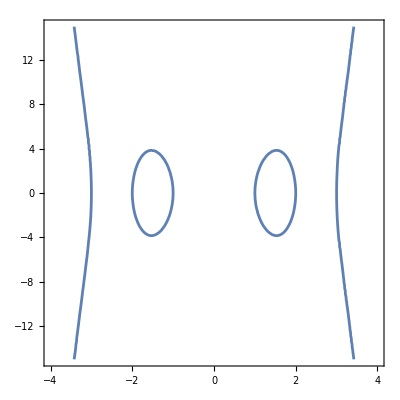

```mathematica
ContourPlot[y^2==(x^2-1)(x^2-4)(x^2-9),{x,-4,4},{y,-15,15}]
```

```mathematica
e1
```

-((-1+(1-l1-l2)^4) (-c1/c2+(1-l1-l2)^4) (-(c1 (-1+c2))/((-1+c1) c2)+(1-l1-l2)^4))+(l1+l2-2 l1 l2)^2

```mathematica
e1/.{c2->1/c1}//Factor
```

-c1^3+c1 x^2-c1^2 x^2+c1^3 x^2+x^4-c1 x^4+c1^2 x^4-x^6+y^2

```mathematica
v1=Sqrt[c2(c1-1)/(c1-c2)]
```

√(((-1+c1) c2)/(c1-c2))

```mathematica
v2=Sqrt[c1(c2-1)/(c2-c1)]
```

√((c1 (-1+c2))/(-c1+c2))

```mathematica
Y^2-X(X-1)(X-c1)/.{X->v1^2(x^2-(c1(c2-1)/(c2 (c1-1)))),Y->v1^3y}//Factor
```

((-1+c1)^2 c2 (-c1^2+c1^2 c2+c1^2 x^2+2 c1 c2 x^2-2 c1^2 c2 x^2-c1 c2^2 x^2-2 c1 c2 x^4+c1^2 c2 x^4-c2^2 x^4+2 c1 c2^2 x^4+c2^2 x^6-c1 c2^2 x^6-c2^2 y^2+c1 c2^2 y^2))/(c1-c2)^3

```mathematica
(-c1^2+c1^2 c2+c1^2 x^2+2 c1 c2 x^2-2 c1^2 c2 x^2-c1 c2^2 x^2-2 c1 c2 x^4+c1^2 c2 x^4-c2^2 x^4+2 c1 c2^2 x^4+c2^2 x^6-c1 c2^2 x^6)//Simplify
```

(-1+x^2) (c2^2 x^4+c1 c2 x^2 (-2+c2-c2 x^2)+c1^2 (1+c2 (-1+x^2)))